This document is long enough that it is annoying to have all the sections open at once.

CDF users: look through the menu items to find out how to expand sections. Alternatively, the shortcut should be Ctrl+‘
Mathematica users: I recommend enabling “Preferences>Interface>Show open/close icon for cell groups” to help with section management.

### Init

Macro to help with exporting figures.

```mathematica
$doExport=True;
exportme[name_,opt:OptionsPattern[Export]][fig_]:=(SetDirectory[NotebookDirectory[]];
If[$doExport,
Export["../fig/"<>name<>".pdf",fig,opt];Export["../fig/"<>name<>".png",fig,opt]];fig)
```

Symbolic assumptions used globally.

```mathematica
$Assumptions=α1>0&&β1>0&&α2>0&&α3>0&&β2>0&&x>0&&σx>0&&σy>0&&σxy>0&&α>ξ&&β>ξ&&α>0&&ξ>0&&β>0
```

α1>0&&β1>0&&α2>0&&α3>0&&β2>0&&x>0&&σx>0&&σy>0&&σxy>0&&α>ξ&&β>ξ&&α>0&&ξ>0&&β>0

### Priors and Posteriors

#### Uncorrelated

Uncorrelated prior and posterior for a product Poisson likelihood:

```mathematica
prior1[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=ProductDistribution[
GammaDistribution[N[μx^2/σx^2],(μx/σx^2)^-1],
GammaDistribution[N[μy^2/σy^2],(μy/σy^2)^-1]
]
priorpdf1[α_,β_,μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=PDF[GammaDistribution[N[μx^2/σx^2],(μx/σx^2)^-1],α]*PDF[GammaDistribution[N[μy^2/σy^2],(μy/σy^2)^-1],β]
posterior1[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=ProductDistribution[GammaDistribution[N[μx^2/σx^2]+Total[xdat],(μx/σx^2+Length[xdat])^-1],GammaDistribution[N[μy^2/σy^2]+Total[ydat],(μy/σy^2+Length[ydat])^-1]]
posteriorpdf1[α_,β_,μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=PDF[GammaDistribution[N[μx^2/σx^2]+Total[xdat],(μx/σx^2+Length[xdat])^-1],α]*PDF[GammaDistribution[N[μy^2/σy^2]+Total[ydat],(μy/σy^2+Length[ydat])^-1],β]
```

#### Correlated Mixture weights

For correlated version, first solve for the gamma distribution parameters in terms of desired means and covariances.

```mathematica
soln=First@Solve[{
x==α1/β1+α3,
y==α2/β2+α3,
σx==α1/β1^2+α3,
σy==α2/β2^2+α3,
σxy==α3
},{α1,α2,α3,β1,β2}]
```

{α1→-(x-σxy)^2/(-σx+σxy),α2→-(y-σxy)^2/(σxy-σy),α3→σxy,β1→(-x+σxy)/(-σx+σxy),β2→(-y+σxy)/(σxy-σy)}

Posterior mixture weights from Karlis and Tsiamyrtzis:

```mathematica
pstar[μx_,σx_,μy_,σy_,σxy_]:=N@With[{α1=-(μx-σxy)^2/(-σx^2+σxy),α2=-(μy-σxy)^2/(σxy-σy^2),α3=σxy,β1=(-μx+σxy)/(-σx^2+σxy),β2=(-μy+σxy)/(σxy-σy^2)},β1^α1 β2^α2/(Gamma[α1]Gamma[α2]Gamma[α3])]
weights[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=(#/Total[#])&@Module[
{c,v,s,S,ss,n=Length@xdat,α1=-(μx-σxy)^2/(-σx^2+σxy),α2=-(μy-σxy)^2/(σxy-σy^2),α3=σxy,β1=(-μx+σxy)/(-σx^2+σxy),β2=(-μy+σxy)/(σxy-σy^2)},
v[r_,m_]:=v[r,m]=(Factorial[xdat[[m]]-r]Factorial[ydat[[m]]-r]Factorial[r])^-1;
s[m_]:=s[m]=Min[{xdat[[m]],ydat[[m]]}];
S[kk_]:=S[kk]=Sum[s[m],{m,kk}];
ss[m_]:=ss[m]=Min[{s[m],S[m-1]}];
c[k_,n_]:=c[k,n]=If[n==1,
v[k,n],
Sum[v[r,n]*c[k-r,n-1],{r,Max[0,k-ss[n]],Min[k,ss[n]]}]
];
pstar[μx,σx,μy,σy,σxy]Table[c[k,n]Gamma[α1-k+Total[xdat]]Gamma[α2-k+Total[ydat]]Gamma[α3+k]((n+β1)(n+β2)/(n+1))^k,{k,S[n]}]
]
relevantWeights[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=Module[{w=weights[μx,σx,μy,σy,σxy,xdat,ydat],indeces},
indeces=Pick[Range[Length@w],w,_?(#>Max[w]/50&)];
{indeces-1,#/Total[#]&@w[[indeces]]}
]
```

Look at what the weights of a posterior look like:

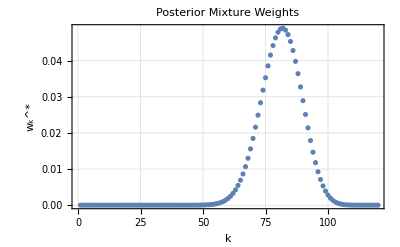

```mathematica
exportme["bivar-posterior-mixture-weights"]@ListPlot[weights[207,40,140,15,90,{220},{120}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[Text["Posterior Mixture Weights"],15],FrameLabel->(Style[Text[#],13]&/@{"k","w_k^*"})]
```

Test the relevant weights function which throws out the small weights for efficiency:

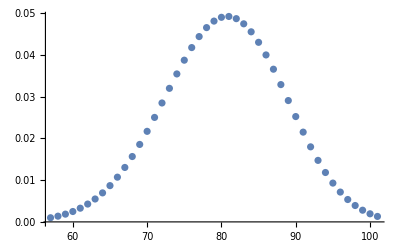

```mathematica
ListPlot[relevantWeights[207,40,140,15,90,{220},{120}]ᵀ,PlotRange->All]
```

#### Sidetrack calculations

If there is only one sample taken, the posterior simplifies a bit. Calculate the same weights in this case: (formula derived below)

```mathematica
w[μx_,σx_,μy_,σy_,σxy_,x_,y_]:=With[{α1=N@-(μx-σxy)^2/(-σx^2+σxy),α2=N@-(μy-σxy)^2/(σxy-σy^2),α0=N@σxy,β1=N@((-μx+σxy)/(-σx^2+σxy)),β2=N@((-μy+σxy)/(σxy-σy^2))},Table[(2^-k ((1+β1) (1+β2))^k Gamma[1+x] Gamma[1+y] Gamma[k+α0] Gamma[-k+x+α1] Gamma[-k+y+α2] Sin[π (x+α1)] Sin[π (y+α2)])/(π^2 k! (-k+x)! (-k+y)! Gamma[α0] HypergeometricPFQRegularized[{-x,-y,α0},{1-x-α1,1-y-α2},1/2 (1+β1) (1+β2)]),{k,1,Min[x,y]}]]
```

Verify that the above sums to unity:

```mathematica
Sum[(2^-k ((1+β1) (1+β2))^k Gamma[1+x] Gamma[1+y] Gamma[k+α0] Gamma[-k+x+α1] Gamma[-k+y+α2] Sin[π (x+α1)] Sin[π (y+α2)])/(π^2 k! (-k+x)! (-k+y)! Gamma[α0] HypergeometricPFQRegularized[{-x,-y,α0},{1-x-α1,1-y-α2},1/2 (1+β1) (1+β2)]),{k,0,Min[x,y]}]//FullSimplify
```

1

Find the normalized sum of the formula with n=1:

```mathematica
Sum[(β1^α1 β2^α2 Gamma[α1-k+x]Gamma[α2-k+y]Gamma[α0+k])/((x-k)!(y-k)!k!Gamma[α1]Gamma[α2]Gamma[α0])(((1+β1)(1+β2))/2)^k,{k,0,Min[x,y]}]//FullSimplify
```

(π^2 β1^α1 β2^α2 Csc[π (x+α1)] Csc[π (y+α2)] HypergeometricPFQRegularized[{-x,-y,α0},{1-x-α1,1-y-α2},1/2 (1+β1) (1+β2)])/(Gamma[1+x] Gamma[1+y] Gamma[α1] Gamma[α2])

Now if we divide each term we get, which was the first formula of this section:

```mathematica
((β1^α1 β2^α2 Gamma[α1-k+x]Gamma[α2-k+y]Gamma[α0+k])/((x-k)!(y-k)!k!Gamma[α1]Gamma[α2]Gamma[α0])(((1+β1)(1+β2))/2)^k)/((π^2 β1^α1 β2^α2 Csc[π (x+α1)] Csc[π (y+α2)] HypergeometricPFQRegularized[{-x,-y,α0},{1-x-α1,1-y-α2},1/2 (1+β1) (1+β2)])/(Gamma[1+x] Gamma[1+y] Gamma[α1] Gamma[α2]))//FullSimplify
```

(2^-k ((1+β1) (1+β2))^k Gamma[1+x] Gamma[1+y] Gamma[k+α0] Gamma[-k+x+α1] Gamma[-k+y+α2] Sin[π (x+α1)] Sin[π (y+α2)])/(π^2 k! (-k+x)! (-k+y)! Gamma[α0] HypergeometricPFQRegularized[{-x,-y,α0},{1-x-α1,1-y-α2},1/2 (1+β1) (1+β2)])

It turns out that this “simplified” formula for n=1 is not less expensive, although no effort has been made to optimize either case.

```mathematica
w[207,400,140,250,90,220,120];//Timing
weights[207,400,140,250,90,{221},{120}];//Timing
```

{0.06,Null}

{0.012,Null}

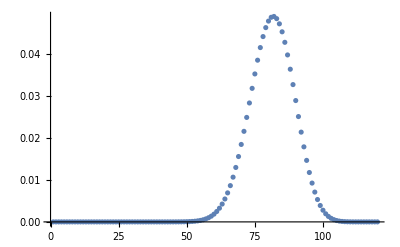

-Graphics-

```mathematica
ListPlot[w[207,40,140,15,90,220,120],PlotRange->All]
ListPlot[weights[207,40,140,15,90,{220},{120}],PlotRange->All]
```

#### Compiled Version

Write a compiled version of the function to speed things up:

```mathematica
w2=Compile[{{μx,_Real},{σx,_Real},{μy,_Real},{σy,_Real},{σxy,_Real},{x,_Real},{y,_Real}},Module[{p,out,indeces,max,α1=-(μx-σxy)^2/(-σx^2+σxy),α2=-(μy-σxy)^2/(σxy-σy^2),α0=σxy,β1=(-μx+σxy)/(-σx^2+σxy),β2=(-μy+σxy)/(σxy-σy^2)},
p=Exp@Table[
α1 Log[β1]+α2 Log[β2]+LogGamma[α1-k+x]+LogGamma[α2-k+y]+LogGamma[α0+k]
+k Log[((1+β1)(1+β2))/2]
-LogGamma[x-k+1]-LogGamma[y-k+1]-LogGamma[k+1]-LogGamma[α1]-LogGamma[α2]-LogGamma[α0]
,
{k,0,Min[x,y]}];
p=p/Total[p];
max=Max[p];
out=Transpose[{Range[0,Min[x,y]],p}];
Select[out,#[[2]]>max/50&]ᵀ
]
];
```

This version is quite a bit faster.

```mathematica
w[207,400,140,250,90,220,120];//AbsoluteTiming
w2[207,400,140,250,90,220,120];//AbsoluteTiming
weights[207,400,140,250,90,{221},{125}];//AbsoluteTiming
```

{0.062464,Null}

{0.001556,Null}

{0.006053,Null}

Check that it matches the previous function too:

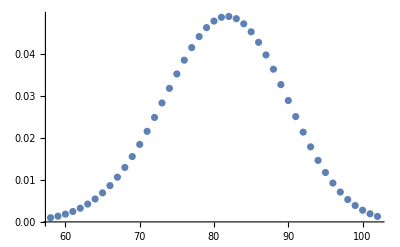

-Graphics-

```mathematica
ListPlot[w2[207,40,140,15,90,220,120]ᵀ,PlotRange->All]
ListPlot[relevantWeights[207,40,140,15,90,List@220,List@120]ᵀ,PlotRange->All]
```

#### Correlated distributions

Now make priors and posteriors for the bivariate Poisson likelihood:

```mathematica
prior2[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=Module[{θ1,θ2,θ3},TransformedDistribution[
{θ1+θ3,θ2+θ3},
{θ1\[Distributed]GammaDistribution[N[-(μx-σxy)^2/(-σx^2+σxy)],((-μx+σxy)/(-σx^2+σxy))^-1],
θ2\[Distributed]GammaDistribution[N[-(μy-σxy)^2/(σxy-σy^2)],((-μy+σxy)/(σxy-σy^2))^-1],
θ3\[Distributed]GammaDistribution[N[σxy],1]}
]]
priorpdf2[α_,β_,μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=NIntegrate[PDF[GammaDistribution[N[-(μx-σxy)^2/(-σx^2+σxy)],((-μx+σxy)/(-σx^2+σxy))^-1],α-ξ]*PDF[GammaDistribution[N[-(μy-σxy)^2/(σxy-σy^2)],((-μy+σxy)/(σxy-σy^2))^-1],β-ξ]*PDF[GammaDistribution[N[σxy],1],ξ],{ξ,0,3*μx}]
posterior2[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=Module[{θ1,θ2,θ3,w,idxs,α1,α2,α3,β1,β2,n},
α1=-N@((μx-σxy)^2/(-σx^2+σxy));α2=-N@((μy-σxy)^2/(σxy-σy^2));α3=N@σxy;β1=N@((-μx+σxy)/(-σx^2+σxy));β2=N@((-μy+σxy)/(σxy-σy^2));
n=Length@xdat;
{idxs,w}=relevantWeights[μx,σx,μy,σy,σxy,xdat,ydat];
TransformedDistribution[
{θ1+θ3,θ2+θ3},
{θ1,θ2,θ3}\[Distributed]MixtureDistribution[w,
Table[ProductDistribution[
GammaDistribution[α1-k+Total[xdat],(β1+n)^-1],
GammaDistribution[α2-k+Total[ydat],(β2+n)^-1],
GammaDistribution[α3+k,(1+n)^-1]
],{k,idxs}]
]]
]
posteriorpdf2[α_,β_,μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=Module[{θ1,θ2,θ3,w,idxs,α1,α2,α3,β1,β2,n},
α1=-N@((μx-σxy)^2/(-σx^2+σxy));α2=-N@((μy-σxy)^2/(σxy-σy^2));α3=N@σxy;β1=N@((-μx+σxy)/(-σx^2+σxy));β2=N@((-μy+σxy)/(σxy-σy^2));
n=Length@xdat;
{idxs,w}=relevantWeights[μx,σx,μy,σy,σxy,xdat,ydat];
Sum[w[[k]]NIntegrate[Times[
PDF[GammaDistribution[α1-k+Total[xdat],(β1+n)^-1],α-ξ],
PDF[GammaDistribution[α2-k+Total[ydat],(β2+n)^-1],β-ξ],
PDF[GammaDistribution[α3+k,(1+n)^-1],ξ]
],{ξ,0,3*μx}],
{k,Length@w}
]
]

ClearAll@priorkde2;
priorkde2[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=priorkde2[μx,σx,μy,σy,σxy,xdat,ydat]=KernelMixtureDistribution[RandomVariate[prior2[μx,σx,μy,σy,σxy,xdat,ydat],1000],3]
priorpdfkde2[α_,β_,μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=PDF[priorkde2[μx,σx,μy,σy,σxy,xdat,ydat],{α,β}]

ClearAll@posteriorkde2;
posteriorkde2[μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=posteriorkde2[μx,σx,μy,σy,σxy,xdat,ydat]=KernelMixtureDistribution[RandomVariate[posterior2[μx,σx,μy,σy,σxy,xdat,ydat],1000],3]
posteriorkdepdf2[α_,β_,μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_]:=PDF[posteriorkde2[μx,σx,μy,σy,σxy,xdat,ydat],{α,β}]
```

Kernel density version is faster to evaluate:

```mathematica
posteriorpdf2[200,150,207,40,140,15,90,{220,175,180},{125,130,120}]//Timing
posteriorkdepdf2[200,150,207,40,140,15,90,{220,175,180},{125,130,120}]//Timing
```

{1.732,0.000161133}

{0.704,0.000056849}

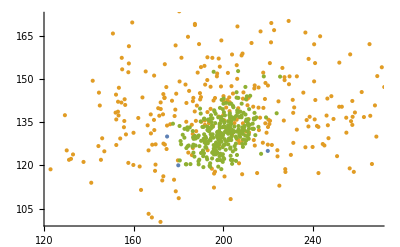

```mathematica
ListPlot[{
{{220,175,180},{125,130,120}}ᵀ,
RandomVariate[prior2[207,40,140,15,90,{220,175,180},{125,130,120}],300],
RandomVariate[posterior2[207,40,140,15,90,{220,175,180},{125,130,120}],300]
}]
```

### Plots

```mathematica
makeEllipse[p_,mat_]:=Module[{d,v},{d,v}=Eigensystem[mat];Rotate[Ellipsoid[p,Sqrt@d],ArcTan@@(First@v)]]
plotcontour[distpdf_,dist_,μx_,σx_,μy_,σy_,σxy_,xdat_,ydat_,opt:OptionsPattern[ListContourPlot]]:=Module[{data,area,qu,pdf,num,stds,αmin,αmax,αstep,βmin,βmax,βstep,fig,t,epilog,options,mean,covmatfun,cov},
num=20;
stds=2;
{αmin,αmax,αstep}={μx-stds*σx,μx+stds*σx,2*stds*σx/num};
{βmin,βmax,βstep}={μy-stds*σy,μy+stds*σy,2*stds*σy/num};

epilog=If[FreeQ[{opt},Epilog],{},{Epilog}/.{opt}];
options=Sequence@@Cases[{opt},_?(FreeQ[#,Epilog]&)];

(*ListContourPlot is fastest with rectangle of points.*)
data=Table[distpdf[α,β,μx,σx,μy,σy,σxy,xdat,ydat],{α,αmin,αmax,αstep},{β,βmin,βmax,βstep}]ᵀ;

covmatfun[dat_]:={{Variance[dat[[All,1]]],Covariance@@(datᵀ)},{Covariance@@(datᵀ),Variance[dat[[All,2]]]}};
{mean,cov}={Mean[#],covmatfun[#]}&@RandomVariate[dist[μx,σx,μy,σy,σxy,xdat,ydat],10^4];
area=π (Times@@Sqrt[Eigenvalues@cov]);
Print@area;
qu=makeEllipse[mean,4.6cov];

fig=ListContourPlot[
data,
options,
DataRange->{{αmin,αmax},{βmin,βmax}},
PlotRange->All,
FrameLabel->{"α","β"},
ImageSize->350,
Epilog->{
Opacity[0],EdgeForm[{Thick,Black,Dashed}],qu,
Opacity[1],Red,PointSize[0.03],Point/@({xdat,ydat}ᵀ),
(*Black,Text["A="<>ToString@area,mean,{Left,Top},Background->LightRed],*)
epilog
}
];

fig
]
label[txt_]:=Text[Style[txt,20,White],Scaled[{0.95,0.9}],{1,0}]
```

```mathematica
With[{μx=200,μy=120,σx=20,σy=15,σxy=100,xdat={170},ydat={100}},
fig1=GraphicsRow[{
plotcontour[priorpdf1,prior1,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorpdf1,posterior1,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->
label["Posterior"]]
}];
fig2=GraphicsRow[{
plotcontour[priorpdf2,prior2,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorkdepdf2,posterior2,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->label["Posterior"]]
}];
]
```

944.888

287.422

905.088

220.3

```mathematica
label2[txt_]:=Graphics[Rotate[Style[Text[txt],20],π/2],ImageSize->{18,300}];
exportme["bivar-correlated-update"]@Grid[{{label2@"Uncorrelated",fig1},{label2["Correlated"],fig2}},Dividers->All,Spacings->3]
```

-Graphics-

```mathematica
With[{μx=200,μy=120,σx=20,σy=15,σxy=100,xdat={230},ydat={100}},
fig3=GraphicsRow[{
plotcontour[priorpdf1,prior1,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorpdf1,posterior1,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->
label["Posterior"]]
}];
fig4=GraphicsRow[{
plotcontour[priorpdf2,prior2,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorkdepdf2,posterior2,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->label["Posterior"]]
}];
]
```

951.218

318.6

909.32

250.584

```mathematica
label2[txt_]:=Graphics[Rotate[Style[Text[txt],20],π/2],ImageSize->{18,300}];
exportme["bivar-anticorrelated-update"]@Grid[{{label2@"Uncorrelated",fig3},{label2["Correlated"],fig4}},Dividers->All,Spacings->3]
```

-Graphics-

```mathematica
With[{μx=2000,μy=1200,σx=200,σy=150,σxy=1000,xdat={1700},ydat={1000}},
fig5=GraphicsRow[{
plotcontour[priorpdf1,prior1,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorpdf1,posterior1,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->
label["Posterior"]]
}];
fig6=GraphicsRow[{
plotcontour[priorpdf2,prior2,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorkdepdf2,posterior2,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->label["Posterior"]]
}];
]
```

93058.2

3982.04

94795.3

2365.48

```mathematica
label2[txt_]:=Graphics[Rotate[Style[Text[txt],20],π/2],ImageSize->{18,300}];
exportme["bivar-correlated-update-large"]@Grid[{{label2@"Uncorrelated",fig5},{label2["Correlated"],fig6}},Dividers->All,Spacings->3]
```

-Graphics-

```mathematica
With[{μx=2000,μy=1200,σx=200,σy=150,σxy=1000,xdat={2300},ydat={1000}},
fig7=GraphicsGrid[{{
plotcontour[priorpdf1,prior1,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorpdf1,posterior1,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->
label["Posterior"]]
}}];
fig8=GraphicsGrid[{{
plotcontour[priorpdf2,prior2,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorkdepdf2,posterior2,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->label["Posterior"]]
}}];
]
```

94397.3

4558.35

92192.3

2945.18

```mathematica
label2[txt_]:=Graphics[Rotate[Style[Text[txt],20],π/2],ImageSize->{18,300}];
exportme["bivar-anticorrelated-update-large"]@Grid[{{label2@"Uncorrelated",fig7},{label2["Correlated"],fig8}},Dividers->All,Spacings->3]
```

-Graphics-

```mathematica
With[{μx=2000,μy=1200,σx=2000,σy=1500,σxy=0,xdat={2300},ydat={1000}},
GraphicsGrid[{{
plotcontour[priorpdf1,prior1,μx,σx,μy,σy,σxy,{},{},Epilog->label["Prior"]],
plotcontour[posteriorpdf1,posterior1,μx,σx,μy,σy,σxy,xdat,ydat,Epilog->
label["Posterior"]]
}}]
]
```

9.46764×10^6

4672.52

-Graphics-

-Graphics-